```mathematica
(*一*）
(*1*)
u[t_,T_]:=Exp[-t^2/T^2+I ω t]/.ω->200 Pi;
Manipulate[Plot[{Abs[u[t,T]]^2,PlotRange->All},{t,-0.1,0.1}],{T,0.01,0.1}]
Manipulate[Plot[{Arg[u[t,T]],PlotRange->All},{t,-0.1,0.1}],{T,0.01,0.1}]
```

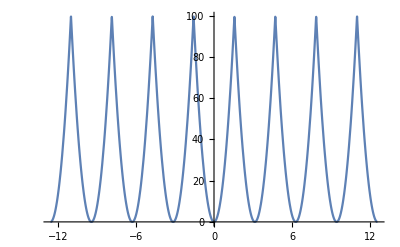

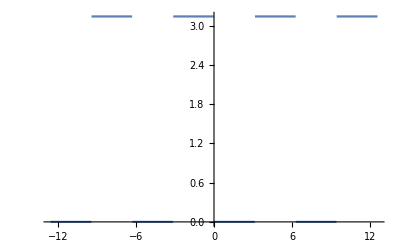

```mathematica
(*2*)
Clear["`*"];
u[t_]:=TriangleWave[{-10,10},t/(2 Pi)];(*confuse*)
Plot[{Abs[u[t]]^2,PlotRange->All},{t,-4Pi,4 Pi}](*confuse*)
Plot[{Arg[u[t]],PlotRange->All},{t,-4 Pi,4 Pi}]
```

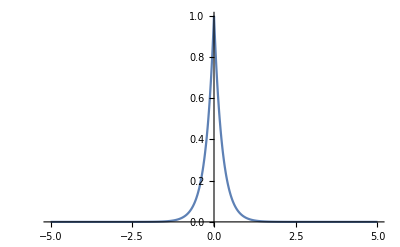

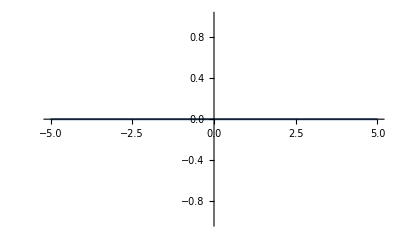

```mathematica
(*3*)
Clear["`*"];
u[t_]:=Exp[-2 Abs[t]];
Plot[Abs[u[t]]^2,{t,-5,5},PlotRange->All]
Plot[Arg[u[t]],{t,-5,5},PlotRange->All]
```

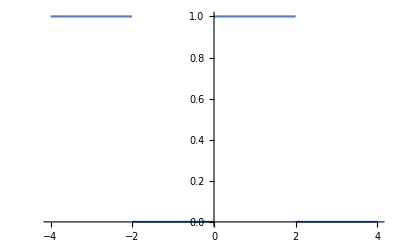

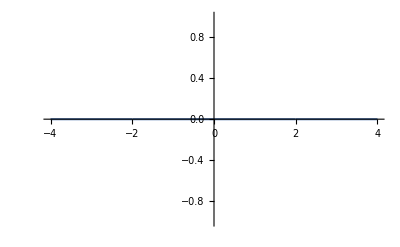

```mathematica
(*4*)
Clear["`*"];
u[t_]:=UnitStep[Sin[Pi/2 t]];
Plot[Abs[u[t]]^2,{t,-4,4},PlotRange->All]
Plot[Arg[u[t]],{t,-4,4},PlotRange->All]
```

```mathematica
(*5*)
Clear["`*"];
u[t_]:=Exp[-t^2/T^2+I ω t] Exp[I t^2/T^2]/.ω->200 Pi;
Manipulate[Plot[{Abs[u[t,T]]^2,PlotRange->All},{t,-0.1,0.1}],{T,0.01,0.1}]
Manipulate[Plot[{Arg[u[t,T]],PlotRange->All},{t,-0.1,0.1}],{T,0.01,0.1}]
```

```mathematica
(*6*)
Clear["`*"];
u1[t_,T_]:=Exp[-t^2/T^2+I ω0 t] Exp[I t Sum[Sin[n ω t],{n,0,3}]]/.{ω0->200 Pi,ω->Pi};
u2[t_,T_]:=Exp[-t^2/T^2+I ω0 t] Exp[I t Sum[Sin[n ω t],{n,0,3}]]/.{ω0->200 Pi,ω->Pi};
Manipulate[Plot[{Abs[u1[t,T]]^2,PlotRange->All},{t,-0.1,0.1}],{T,0.01,0.1}]
Manipulate[Plot[{Abs[u2[t,T]]^2,PlotRange->All},{t,-0.1,0.1}],{T,0.01,0.1}]
Manipulate[Plot[{Arg[u1[t,T]],PlotRange->All},{t,-0.1,0.1}],{T,0.01,0.1}]
Manipulate[Plot[{Arg[u2[t,T]],PlotRange->All},{t,-0.1,0.1}],{T,0.01,0.1}]
```

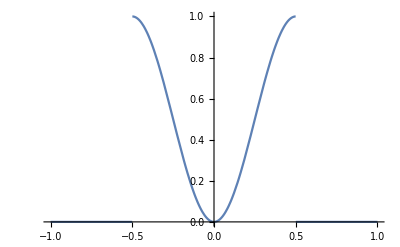

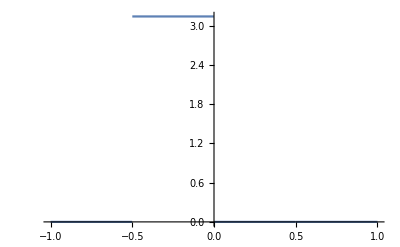

```mathematica
(*7*)
u[t_]:=UnitBox[t] Sin[Pi t];
Plot[Abs[u[t]]^2,{t,-1,1},PlotRange->All]
Plot[Arg[u[t]],{t,-1,1},PlotRange->All]
```

```mathematica
(*8*)
```

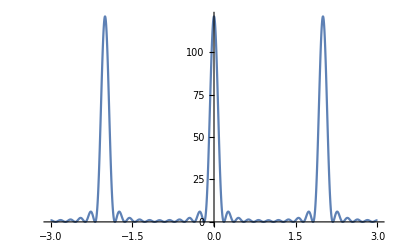

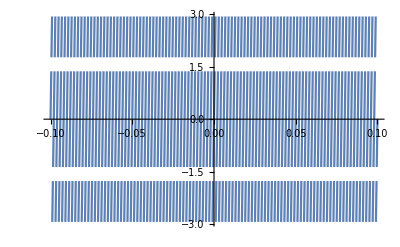

```mathematica
u[t_]:=Sum[Exp[I(1000 Pi+n Pi)t],{n,-5,5}];
Plot[Abs[u[t]]^2,{t,-3,3},PlotRange->All]
Plot[Arg[u[t]],{t,-0.1,0.1},PlotRange->All]
```

```mathematica
(*二*)
Clear["`*"];
u1[t_,T_]:=Exp[-t^2/T^2+I 100 Pi t] Exp[I t^2/T^2];
u2[t_]:=UnitBox[t] Sin[Pi t];
u3[t_]:=Sum[Exp[I(1000Pi+n Pi)t],{n,-5,5}];
(*能量*)
E1=Integrate[Abs[u1[t,T]]^2,{t,-Infinity,Infinity}]
E2=Integrate[Abs[u2[t]]^2,{t,-Infinity,Infinity}]
E3=Integrate[Abs[u3[t]]^2,{t,-Infinity,Infinity}]
```

ConditionalExpression[(√(π/2))/(√Re[(1-ⅈ)/T^2]), Re[-(1-ⅈ)/T^2]<0&&Re[(1-ⅈ)/T^2]≥0]

1/2

∞

```mathematica
(*重心*)
G1=Integrate[t Abs[u1[t,T]^2],{t,-Infinity,Infinity}]/E1
G2=Integrate[t Abs[u2[t]^2],{t,-Infinity,Infinity}]/E2
G1=Integrate[t Abs[u3[t]^2],{t,-Infinity,Infinity}]/E3
```

ConditionalExpression[0, ]

0

Integrate::idiv: t Abs[1+ⅇ^(ⅈ π t)+ⅇ^(2 ⅈ π t)+ⅇ^(3 ⅈ π t)+ⅇ^(4 ⅈ π t)+ⅇ^(5 ⅈ π t)+ⅇ^(6 ⅈ π t)+ⅇ^(7 ⅈ π t)+ⅇ^(8 ⅈ π t)+ⅇ^(9 ⅈ π t)+«1»]^2 的积分在 {-∞,∞} 上不收敛.

$Aborted

```mathematica
0
```

Integrate::idiv: t Abs[1+ⅇ^(ⅈ π t)+ⅇ^(2 ⅈ π t)+ⅇ^(3 ⅈ π t)+ⅇ^(4 ⅈ π t)+ⅇ^(5 ⅈ π t)+ⅇ^(6 ⅈ π t)+ⅇ^(7 ⅈ π t)+ⅇ^(8 ⅈ π t)+ⅇ^(9 ⅈ π t)+«1»]^2 的积分在 {-∞,∞} 上不收敛.

```mathematica
(*二阶矩宽度*)
W1=Integrate[t^2 Abs[u1[t,T]^2],{t,-Infinity,Infinity}]/E1
W2=Integrate[t^2 Abs[u2[t]^2],{t,-Infinity,Infinity}]/E2
W1=Integrate[t^2 Abs[u3[t]^2],{t,-Infinity,Infinity}]/E3
```

ConditionalExpression[(√Re[(1-ⅈ)/T^2])/(√2 Re[(2-2 ⅈ)/T^2]^(3/2)), ]

(6+π^2)/(12 π^2)

Infinity::indet: 碰到不定表达式 0 ∞.

Indeterminate

```mathematica
(*幅度变化率*)
dw1=D[Abs[u1[t,T]],t]/.t->0.1
dw2=D[Abs[u2[t]],t]/.t->0.1
dw2=D[Abs[u3[t]],t]/.t->0.1
(*相位变化率*)
```

ⅇ^(-0.1 Im[ω]+Re[-(0.01-0.01 ⅈ)/T^2]) (-ω Im'[0.1 ω]-((0.2-0.2 ⅈ) Re'[-(0.01-0.01 ⅈ)/T^2])/T^2)

2.98783 Abs'[0.309017]

(-79.8961+19835.2 ⅈ) Abs'[6.31375+1.24345×10^-14 ⅈ]

```mathematica
dd1=D[Phase[u1[t,T]],t]/.t->0.1
dd1=D[Phase[u2[t]],t]/.t->0.1
dd1=D[Phase[u3[t]],t]/.t->0.1
```

ⅇ^(-(0.01-0.01 ⅈ)/T^2+(0.+0.1 ⅈ) ω) (-(0.2-0.2 ⅈ)/T^2+ⅈ ω) Phase'[ⅇ^(-(0.01-0.01 ⅈ)/T^2+(0.+0.1 ⅈ) ω)]

2.98783 Phase'[0.309017]

(-79.8961+19835.2 ⅈ) Phase'[6.31375+1.24345×10^-14 ⅈ]

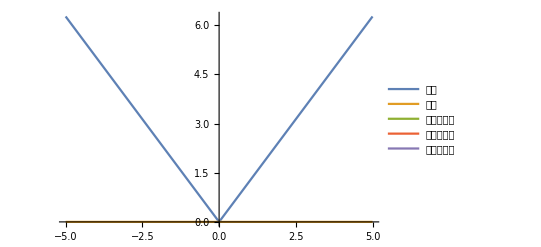

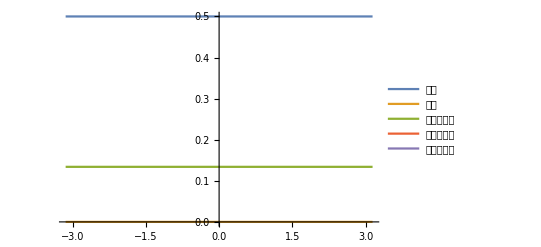

-Graphics-

```mathematica
(*图像*)
Plot[{E1,G1,W1,dw1,dd1},{T,-5,5},PlotRange->All,PlotLegends->{"能量","重心","二阶矩宽度","幅度变化率","相位变化率"}]
Plot[{E2,G2,W2,dw2,dd2},{ω,-Pi,Pi},PlotRange->All,PlotLegends->{"能量","重心","二阶矩宽度","幅度变化率","相位变化率"}]

Plot[{E3,G3,W3,dw3,dd3},{T,-5,5},PlotRange->All,PlotLegends->{"能量","重心","二阶矩宽度","幅度变化率","相位变化率"}]
```